```mathematica
TensorData = ToExpression[Import["C:\\ETH\\Neuro\\GlobalTracking\\GlobalTrackingScripts\\tensor_data.txt"]];
dim=Dimensions[TensorData]
Tensor[i_,j_,k_]:={{TensorData[[i,j,k,1]],TensorData[[i,j,k,2]],TensorData[[i,j,k,3]]},{TensorData[[i,j,k,2]],TensorData[[i,j,k,4]],TensorData[[i,j,k,5]]},{TensorData[[i,j,k,3]],TensorData[[i,j,k,5]],TensorData[[i,j,k,6]]}}
```

{9,9,9,6}

```mathematica
g[{ϕ_,θ_}]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
Initialize[E0init_,αmaxinit_]:={

αmax = αmaxinit;
E0 =E0init;

S= Table[Eigenvectors[Tensor[i,j,k]][[1]],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
(*S=Table[g[{RandomReal[{0,2Pi}],RandomReal[{0,Pi}]}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];*)

A=Association[
Flatten[
Table[{i,j,k,1}->Association[{
"tensor"->Tensor[i,j,k],
"direction"->S[[i,j,k]],
"position" -> {i,j,k},
"neighbors"-> DeleteCases[
Flatten[
Table[{ii,jj,kk,1},
{ii,Max[1,i-1],Min[dim[[1]],i+1]},{jj,Max[1,j-1],Min[dim[[2]],j+1]},{kk,Max[1,k-1],Min[dim[[3]],k+1]}],
2],
{i,j,k,1}],
"forward"->{},
"backward"->{}}],
{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}],3]
];

AppendTo[A,
{}->Association[{
"tensor"->{},
"direction"->{},
"position" -> {},
"neighbors"-> {},
"forward"->{},
"backward"->{}}]
];
}
```

```mathematica
F[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]>0  )&
]

B[spin_]:=Select[
A[spin]["neighbors"],
( (A[#]["position"]-A[spin]["position"]).A[spin]["direction"]<=0  )&
]

Eint[{}]:=0

Eint[spin_]:=Module[{COSα = {},backward,forward},

forward = A[spin]["forward"];
backward = A[spin]["backward"];

If[backward≠{},
AppendTo[COSα,Abs[(A[backward]["position"]-A[spin]["position"]).A[backward]["direction"]]];
AppendTo[COSα,Abs[(A[backward]["position"]-A[spin]["position"]).A[spin]["direction"]]];
];
If[A[spin]["forward"]≠{},
AppendTo[COSα, Abs[(A[forward]["position"]-A[spin]["position"]).A[forward]["direction"]]];AppendTo[COSα, Abs[(A[forward]["position"]-A[spin]["position"]).A[spin]["direction"]]];
];

E0 + Sum[-E0/4.-Log[If[(cosα-Cos[αmax])/(1-Cos[αmax])>0,(cosα-Cos[αmax])/(1-Cos[αmax]),0.]],{cosα,COSα}]
]

Edata[spin_]:=A[spin]["direction"].Inverse[A[spin]["tensor"]].A[spin]["direction"]
```

```mathematica
(*=========================================================================*)
(*========================= CREATE ========================================*)
(*=========================================================================*)

CreateNew[str_,spin_]:=Module[{newposition,newforward,newbackward,newID},

If[str == "forward",

newposition = Round[A[spin]["position"]+A[spin]["direction"]];

If[1<=newposition[[1]]≤dim[[1]]&&1<=newposition[[2]]≤dim[[2]]&&1<=newposition[[3]]≤dim[[3]],

newID = Length[Select[A,#["position"]==newposition&]]+1;

AppendTo[A,
Append[newposition,newID]->Association[{
"tensor"->A[Append[newposition,newID-1]]["tensor"],
"direction"->A[spin]["direction"],
"position" -> newposition,
"neighbors"-> A[Append[newposition,newID-1]]["neighbors"],
"forward"->{},
"backward"->spin}]
];

newforward=Append[newposition,newID];
A[spin]["forward"] = newforward;

Table[AppendTo[A[n]["neighbors"],newforward],{n,A[newforward]["neighbors"]}];

,
Null;
]

,(*=======================================================*)

newposition = Round[A[spin]["position"]-A[spin]["direction"]];

If[1<=newposition[[1]]≤dim[[1]]&&1<=newposition[[2]]≤dim[[2]]&&1<=newposition[[3]]≤dim[[3]],

newID = Length[Select[A,#["position"]==newposition&]]+1;

AppendTo[A,
Append[newposition,newID]->Association[{
"tensor"->A[Append[newposition,newID-1]]["tensor"],
"direction"->A[spin]["direction"],
"position" -> newposition,
"neighbors"-> A[Append[newposition,newID-1]]["neighbors"],
"forward"->spin,
"backward"->{}}]
];

newbackward=Append[newposition,newID];
A[spin]["backward"] = newbackward;

Table[AppendTo[A[n]["neighbors"],newbackward],{n,A[newbackward]["neighbors"]}];
,
Null;
]
]
]
(*=========================================================================*)
(*========================= ASSOCIATE =====================================*)
(*=========================================================================*)
Associate[spin_]:=Module[{newforward,newbackward,oldforward,oldbackward,E0,E1,p},

newforward= RandomChoice[F[spin]];(*What if newforward = {}? Should not happen for volume spins *)

oldforward =A[spin]["forward"];
oldbackward=A[newforward]["backward"];

E0 = Eint[spin] +  Eint[oldforward] +
	Eint[newforward] + Eint[oldbackward];

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["forward"] = newforward;
A[newforward]["backward"] = spin;

E1 = Eint[spin] +  Eint[newforward] +
	Eint[oldforward] + Eint[oldbackward];

p = Min[1., Exp[E0-E1]];

If[RandomReal[]> p,
A[oldforward]["backward"] = spin;
A[oldbackward]["forward"] = newforward;
A[spin]["forward"] = oldforward;
A[newforward]["backward"] = oldbackward;

(*CreateNew["forward",spin];*)
];

(*========================================*)

newbackward= RandomChoice[B[spin]];

oldforward =A[newbackward]["forward"];
oldbackward=A[spin]["backward"];

E0 = Eint[spin] +  Eint[oldforward] +
	Eint[newbackward] + Eint[oldbackward];

A[oldforward]["backward"] = {};
A[oldbackward]["forward"] = {};
A[spin]["backward"] = newbackward;
A[newbackward]["forward"] = spin;

E1 = Eint[spin] +  Eint[newbackward] +
	Eint[oldforward] + Eint[oldbackward];

p = Min[1., Exp[E0-E1]];

If[RandomReal[{0,1}]> p,
A[oldforward]["backward"] = newbackward;
A[oldbackward]["forward"] = spin;
A[spin]["backward"] = oldbackward;
A[newbackward]["forward"] = oldforward;

(*CreateNew["backward",spin];*)
];
]
(*=========================================================================*)
(*========================= ALIGN  ========================================*)
(*=========================================================================*)
Align[spin_]:=Module[{newdirection,olddirection,E0,E1,p},

olddirection=A[spin]["direction"];
newdirection =  g[RandomReal[{0,2Pi},2]];

E0 = Eint[spin] + Edata[spin];

A[spin]["direction"]=newdirection;

E1 = Eint[spin] + Edata[spin];

p = Min[1., Exp[E0-E1]];

If[RandomReal[]>p,
A[spin]["direction"]=olddirection;
]
]
(*=========================================================================*)
(*=========================================================================*)
```

```mathematica
Energy ={};
Initialize[100.,Pi/2.];
Block[{i,j,k,n,s,N=100},

For[n=1,n≤N,n++,

Energy = Append[Energy,Sum[Eint[{i,j,k,1}]+Edata[{i,j,k,1}],{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}]];

For[i=2,i<dim[[1]],i++,
For[j=2,j<dim[[2]],j++,
For[k=2,k<dim[[3]],k++,
Associate[{i,j,k,1}];
]]]

(*For[i=1,i<=dim[[1]],i++,
For[j=1,j<=dim[[2]],j++,
For[k=1,k<=dim[[3]],k++,
Align[{i,j,k,1}];
]]]*)

];
]
```

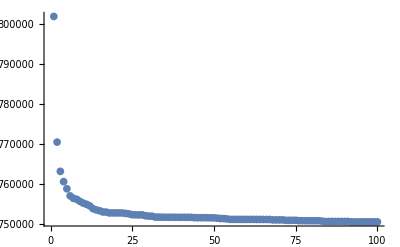

```mathematica
ListPlot[Energy,PlotRange->All]
```

```mathematica
Min[Energy]
```

750491.

```mathematica
Max[Energy]
```

801757.